{1,2,4,5,6,23,1}

{{1},{2},{4},{5},{6},{23},{1}}

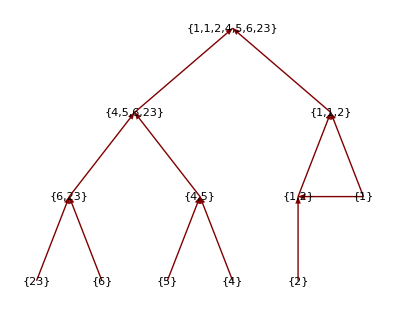

```mathematica
toBeSorted = Input["Enter list ot be sorted (format: {val1,val2,....} )"]
toBeSorted = Table[{toBeSorted[[i]]},{i,1,Length[toBeSorted]}]
(*toBeSorted = {{23},{1},{54},{3},{7},{19},{21}};*)
listLength = Length[toBeSorted];
i=1;
mergeTree = {};
newNodeSet ={};
leftChildren={};
rightChildren={};
While[Length[toBeSorted[[Length[toBeSorted]]]]≠listLength,
If[i== Length[toBeSorted],
newNodeSet = newNodeSet ~Join~ toBeSorted[[i]];
toBeSorted = newNodeSet;
newNodeSet={};
i=1
,
If[i> Length[toBeSorted],
toBeSorted=newNodeSet;
i=1
,
newNode = Sort[toBeSorted[[i]] ~ Join ~ toBeSorted[[i+1]]];
mergeTree = mergeTree ~Join~ { toBeSorted[[i]]->  newNode,toBeSorted[[i+1]] -> newNode};
leftChildren = Append[leftChildren,toBeSorted[[i]]->  newNode];
rightChildren = Append[rightChildren,toBeSorted[[i+1]]->  newNode];
toBeSorted = Append[toBeSorted,newNode];
newNodeSet = newNodeSet ~Join~ newNode;
i+= 2;
]
]
]
newMergeTree = leftChildren ~Join~ rightChildren;
newMergeTree = Reverse[newMergeTree];
TreePlot[newMergeTree, DirectedEdges->True, VertexLabeling->True]
```

```mathematica
RowBox[{"1",",","2",",","3",",","4"}]
```

RowBox[{1,,,2,,,3,,,4}]